# Project report

## SFC×GC recommissioning

D Malan

Department of Chemistry
University of Pretoria

17 December 2019

## Introduction

The aim of this project is to get the SFC×GC into a running state. The column needs to be replaced, after an overheating event.

## Experimental

### GC column

The coaxial heater was removed without undue trouble.

One of the protective clips was embedded on the column, after the incident. I removed it by heating the stainless steel with current from the bench power supply. This melted the plastic, so I could 	slide it in the opposite direction that it had melted in.

Except for some discoloration, the stainless steel of the coaxial heater is undamaged. As expected, however, the column coating has been scorched black.

Surprisingly, the column breakage was not at the overheated spot, but at the inlet end of the coaxial heater, just behind the ferrule. I don’t know enough about capillary column fracture modes to say anything with certainty, but it seems like a tension fracture: I don’t see any signs of crushing.

### GC gas flow

With the coaxial heater out of the oven I took the opportunity to measure carrier gas flow rate. I connected a 1 m length of column to the inlet, and recorded the time it took to fill a given volume of the gas flow meter. I measured this flow at a

```mathematica
file = SystemDialogInput["FileOpen"]
```

C:\Users\fskdm\My PhD\Projects\2019_12_06_SFCxGC Recomissioning\2019_12_17_SFCxGCRecommissioning\2019_12_17_Flow_measurement.xlsx

```mathematica
file = "C:\\Users\\fskdm\\My PhD\\Projects\\2019_12_06_SFCxGC Recomissioning\\2019_12_17_SFCxGCRecommissioning\\2019_12_17_Flow_measurement.xlsx"
```

C:\Users\fskdm\My PhD\Projects\2019_12_06_SFCxGC Recomissioning\2019_12_17_SFCxGCRecommissioning\2019_12_17_Flow_measurement.xlsx

```mathematica
data = Import[file][[1]]; TableForm[data]
```

Head pressure (psi) | Volume (ml) | Time (s) | Time (min) | Flow (ml/min)
8. | 2. | 11.2 | 0.186667 | 10.7143
8. | 2. | 11.11 | 0.185167 | 10.8011
8. | 1.5 | 8.31 | 0.1385 | 10.8303
8. | 2. | 10.99 | 0.183167 | 10.919
12. | 2. | 3.58 | 0.0596667 | 33.5196
12. | 2. | 3.63 | 0.0605 | 33.0579
12. | 2. | 3.61 | 0.0601667 | 33.241
12. | 2. | 3.7 | 0.0616667 | 32.4324
12. | 2. | 3.75 | 0.0625 | 32.
16. | 2. | 2.13 | 0.0355 | 56.338
16. | 10. | 9.91 | 0.165167 | 60.5449
16. | 10. | 11.88 | 0.198 | 50.5051
16. | 2. | 2.07 | 0.0345 | 57.971
16. | 2. | 1.99 | 0.0331667 | 60.3015
20. | 8. | 5.31 | 0.0885 | 90.3955
20. | 8. | 5.38 | 0.0896667 | 89.2193
20. | 8. | 5.33 | 0.0888333 | 90.0563
20. | 8. | 5.32 | 0.0886667 | 90.2256
20. | 10. | 6.73 | 0.112167 | 89.153
7. | 1. | 8.79 | 0.1465 | 6.82594
7. | 1. | 8.55 | 0.1425 | 7.01754
7. | 1. | 8.46 | 0.141 | 7.0922
7. | 1. | 8.46 | 0.141 | 7.0922
7. | 1. | 8.35 | 0.139167 | 7.18563

```mathematica
sdata = Split[data,First[#1]==First[#2]&]
```

{{{Head pressure (psi),Volume (ml),Time (s),Time (min),Flow (ml/min)}},{{8.,2.,11.2,0.186667,10.7143},{8.,2.,11.11,0.185167,10.8011},{8.,1.5,8.31,0.1385,10.8303},{8.,2.,10.99,0.183167,10.919}},{{12.,2.,3.58,0.0596667,33.5196},{12.,2.,3.63,0.0605,33.0579},{12.,2.,3.61,0.0601667,33.241},{12.,2.,3.7,0.0616667,32.4324},{12.,2.,3.75,0.0625,32.}},{{16.,2.,2.13,0.0355,56.338},{16.,10.,9.91,0.165167,60.5449},{16.,10.,11.88,0.198,50.5051},{16.,2.,2.07,0.0345,57.971},{16.,2.,1.99,0.0331667,60.3015}},{{20.,8.,5.31,0.0885,90.3955},{20.,8.,5.38,0.0896667,89.2193},{20.,8.,5.33,0.0888333,90.0563},{20.,8.,5.32,0.0886667,90.2256},{20.,10.,6.73,0.112167,89.153}},{{7.,1.,8.79,0.1465,6.82594},{7.,1.,8.55,0.1425,7.01754},{7.,1.,8.46,0.141,7.0922},{7.,1.,8.46,0.141,7.0922},{7.,1.,8.35,0.139167,7.18563}}}

```mathematica
plotdata = data[[2;;,{1,5}]]
```

{{8.,10.7143},{8.,10.8011},{8.,10.8303},{8.,10.919},{12.,33.5196},{12.,33.0579},{12.,33.241},{12.,32.4324},{12.,32.},{16.,56.338},{16.,60.5449},{16.,50.5051},{16.,57.971},{16.,60.3015},{20.,90.3955},{20.,89.2193},{20.,90.0563},{20.,90.2256},{20.,89.153},{7.,6.82594},{7.,7.01754},{7.,7.0922},{7.,7.0922},{7.,7.18563}}

```mathematica
meandata ={Mean[#[[All,1]]],Mean[#[[All,5]]]}& /@ sdata[[2;;]]
```

{{8.,10.8162},{12.,32.8502},{16.,57.1321},{20.,89.8099},{7.,7.0427}}

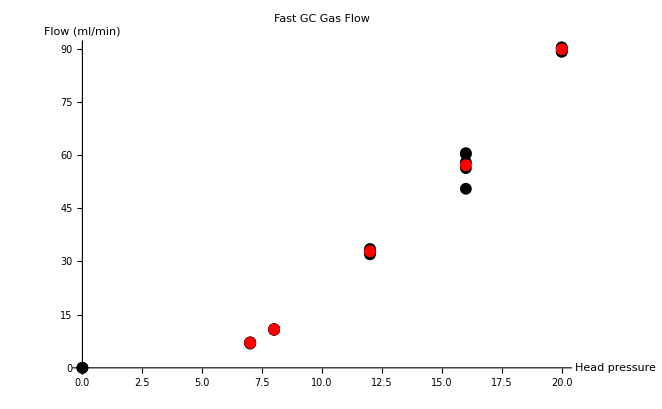

```mathematica
plot = ListPlot[{plotdata, meandata, {{0,0}}}, PlotLabel->"Fast GC Gas Flow", AxesLabel->{"Head pressure", "Flow (ml/min)"}, PlotStyle->{Black, Red}]
```

The shortness of the column and the lowest available pressure from the regulator makes for a rather high GC gas flow rate.

### Column re-installation

I am using a checklist I made on Evernote:

I'd halted reinstallation at this time because I was too tired and risked breaking a column through clumsiness. Then there was the possibility that I’d modify the instrument to programatically ignite the FID flame (see the autoignition project), so I did not continue the installation until I was certain nothing needed done on the Varian.

## Discussion

Hot spot?

## Conclusion

## Recommendations